```mathematica
Clear["GLobals`*"]
```

----- Creamos una función ------
 Module [ { Inicializamos los valores separados por comas } , Función [ ] : = Escribimos la función ]

```mathematica
Module[{a=314159269,c=453806245,m=2^31,z=1000},RndData[]:= (z=Mod[z*a+c,m])/m //N
]
```

```mathematica
RndData[]
```

0.50313

----- Recogemos muestras -----

```mathematica
muestras =Table[RndData[],100000];
```

```mathematica
muestras[[1;;20]]
```

{0.607222,0.243107,0.292092,0.411891,0.145711,0.126371,0.513474,0.0849767,0.498178,0.408791,0.383209,0.169938,0.832972,0.0415893,0.534402,0.599613,0.734372,0.323467,0.528235,0.408409}

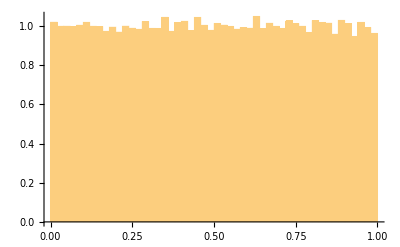

```mathematica
Histogram[muestras,30,PDF]
```

----- Creamos la función exponencial -----

```mathematica
RndExp[rate_]:=-Log[RndData[]]/rate;
```

```mathematica
muestras2=Table[RndExp[100],10000];
```

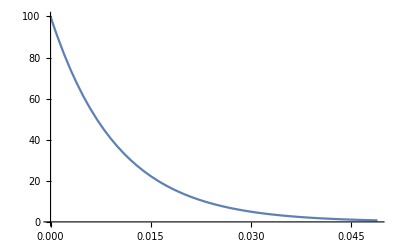

```mathematica
g1=Plot[100*E^(-100*t),{t,0,0.049}]
```

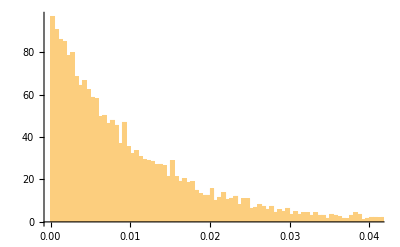

```mathematica
h1=Histogram[muestras2,200,PDF]
```

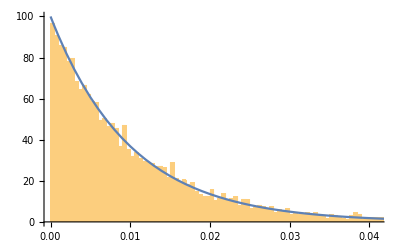

```mathematica
Show [h1,g1]
```

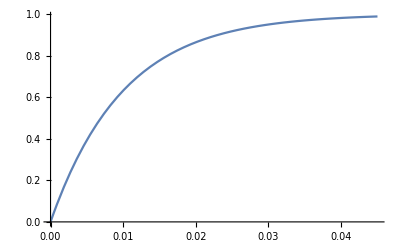

```mathematica
g=Plot[1-E^(-100*t),{t,0,0.045}]
```

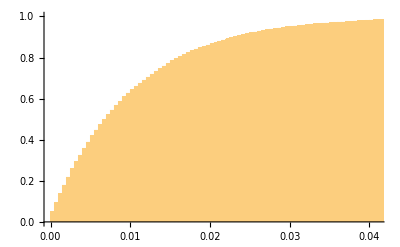

```mathematica
h=Histogram[muestras2,125,CDF]
```

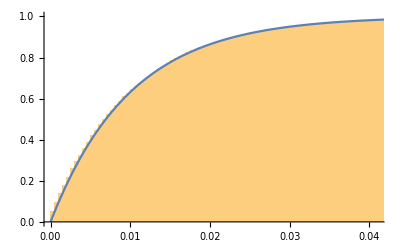

```mathematica
Show[h,g]
```

```mathematica
a={1,2,3,7,3}
```

{1,2,3,7,3}

```mathematica
Join[{a[[1]]},Differences[Accumulate[a]]]
```

{1,2,3,7,3}